```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/limit_cycles/src_mathematica/Ganesh

```mathematica
hbar=197.327053;
Mm=938.858;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]
```

ℏ^2/(2  μ) = 20.7369

Read LEC list (e.g. fitted to two-body scattering length via <<<Fit_Scattering_length.nb>>>)

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
(*LECsNUCL=Import["../LECs_nucl_Rimas-Martin.dat","Table"];
activeLEC=LECsNUCL[[All,{1,2}]][[2;;]];*)
activeLEC=Import["./tmp.dat","Table"];
```

Calculate the dimer wave function in a Gaussian basis rdimer=∑_(i=1)^N c_i·e^(-α_i r^2)

```mathematica
I1=Compile[{lam,b1,b2},(Pi/(2b1+2b2+lam^2))^(3/2)];
I3=Compile[{b1,b2},3 b1 b2 Pi^(3/2)/(2^(1/2)(b1+b2)^(5/2))];
```

```mathematica
ham=Compile[{lam,b1,b2,lec},lec I1[lam,b1,b2]+(1/mh2) I3[b1,b2]];
norm=Compile[{b1,b2},(Pi/(2 b1+2 b2))^(3/2)];
```

```mathematica
ApproxDimerWF[lamd_,dimD_,nbrThreads_,nbrWidthSamples_,minW_,maxW_,minWidthDiff_,verbosity_,σw_:2]:=Block[{LECc,e0,λ=lamd,Δ=minWidthDiff,αmax=maxW,αmin=minW,Nd=dimD,Ns=nbrWidthSamples,Nth=nbrThreads},

LECc=Flatten[Select[activeLEC,#[[1]]==λ&]][[2]];
Print[LECc];
widths={};
rndPrec=5;
Do[

widthLr=Sort[#]&/@RandomReal[{SetPrecision[αmin,rndPrec+1],SetPrecision[αmax,rndPrec+1]},{Ns,Nd},WorkingPrecision->rndPrec];

(*t1=Sort[#]&/@Abs[RandomVariate[NormalDistribution[αmin,σw],{Ns,IntegerPart[Nd/2]}]];
t2=Sort[#]&/@Abs[RandomVariate[NormalDistribution[αmax,σw],{Ns,IntegerPart[Nd/2]}]];

widthLr=ArrayReshape[Flatten[#]&/@Tuples[{t1,t2}],{Nd,Ns}];*)

widthL=Select[widthLr,AllTrue[Select[Tuples[#,2],#[[1]]!=#[[2]]&],Abs[#[[1]]-#[[2]]]>Δ&]&];

AppendTo[widths,widthL];
,{nn,Nth}];

If[verbosity==1,Print["λ = ",λ,"   C_0(λ) = ",LECc,"  #(width-set candidates) = ",Length[Flatten[widths,1]],"  in ",Nth," parallel threads."]];
opti={};
SetSharedVariable[opti];

ta=AbsoluteTime[];
ParallelDo[
widthL=widths[[nt]];
results=0.0;e0=0.0;
optSet={};
Do[
Nd=Length[wi];
hamm=Table[ham[λ,wi[[i]],wi[[j]],LECc],{i,Nd},{j,Nd}];
normm=Table[norm[wi[[i]],wi[[j]]],{i,Nd},{j,Nd}];

{eval,evec}=Eigensystem[{hamm,normm}];

ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
vecsorted=evec[[ord]];

If[(
(eigsorted[[1]]<results)&&
(eigsorted[[1]]>-2.65)&&
(Im[eigsorted[[1]]]==0)&&
(NormTF[Transpose[{vecsorted[[1]],wi}]]>10^-5)&&
(Min[Abs[vecsorted[[1]]]]>10^-2)&&
(ContainsOnly[Sign[vecsorted[[1]]],{1}]||ContainsOnly[Sign[vecsorted[[1]]],{-1}])
),
(*Print[eigsorted[[1]],eigsorted];*)
e0=eigsorted[[1]];
results=eigsorted[[1]];
optSet=Transpose[{vecsorted[[1]],wi}];
]
,{wi,widthL}];
If[verbosity==1,Print["Core ",nt," : ",e0,optSet]];
AppendTo[opti,{e0,optSet}];
,{nt,Nth}];
tb=AbsoluteTime[];

e0=Sort[opti][[1]][[1]];
optSet=Sort[opti][[1]][[2]];
If[verbosity==1,Print["optimum of ",Style[Length[Flatten[widths,1]],Red,Italic,18]," candidate width sets found in Δt = ",Style[tb-ta,Red,Italic,18]," sec.          : E_0 = ",e0]];
(*Print["opt. basis: ",optSet];*)
(*Put[optSet,"dimerWF_"<>ToString[e0]<>".mmo"];
Put[e0,"E0_"<>ToString[e0]<>".mmo"];*)
{e0,optSet}
];
rma=2;rmi=0.;nR=100;
rR=Range[rmi,rma,(rma-rmi)/nR];
```

```mathematica
RiccatiBesselJ=Compile[{z,l},z SphericalBesselJ[l,z]];
RiccatiBesselN=Compile[{z,l},(-1)^l z SphericalBesselY[l,z]];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha=Compile[{ra,ka,la,ha},RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]];

beta=Compile[{rb,kb,lb,hb},RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])];
```

reference: J. Spanier, K.B. Oldham - An Atlas of Functions (1987)

x·j_n(x)=√((π x)/2)J_(n+1/2)(x)=^(x∈C)√((π x)/2)i^(n+1/2) I_(n+1/2)(Re[x])
with
 j_n: spherical Bessel (1st kind)
 J_n: Bessel (1st kind)
 I_n: modified Bessel (1st kind)
 to optimize runtime, we substitute in this implementation -- valid for S-wave scattering, only:
 j_0(i x)=Sinh[x]/x
 and
 j_1(i x)=i x^-1(Cosh[x]-Sinh[x]/x)
 For numerical stability at arguments x>>1, it is curucial to subsitute the following representation:
 e^(-aR^2-bR'^2) Sinh[bRR']=1/2(e^(-aR^2-bR'^2+bRR')-e^(-aR^2-bR'^2-bRR')) and similarly for the hyperbolic cosine;
 Retaining the Sinh built-in function throws, at best, warnings, and yields significantly inaccurate and almost certainly non-sensical results!

```mathematica
NormTF=Compile[{{core,_Real,2}},(Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] Gamma[3/2]/(2 (core[[i]][[2]]+core[[j]][[2]])^(3/2)),{i,Length[core]},{j,Length[core]}]]])^2];

VlocTF=Compile[{r,lam,Cc,Dd,Aa,Bb,Gg,Hh,no},Block[{eta2,eta3,w2,w3},
eta2=(8/Pi^1.5) ((Aa+Bb) (Gg+Hh))^1.5 Cc/(4 (lam Bb+Aa (lam+2 Gg+2 Bb)+lam Hh+2 Bb Hh+Gg (lam+2 Hh))^(3/2));
w2=2 lam (Aa+Hh) (Gg+Bb)/(lam Bb+Aa (lam+2 Gg+2 Bb)+lam Hh+2 Bb Hh+Gg (lam+2 Hh));
eta3=(8/Pi^1.5) ((Aa+Bb) (Gg+Hh))^1.5 Cc/(4(lam Bb+Gg (lam+2 Bb)+lam Hh+2 Bb Hh+Aa (lam+2 Gg+2 Hh))^(3/2));
w3=2 lam (Aa+Bb) (Gg+Hh)/(lam Bb+Gg (lam+2 Bb)+lam Hh+2 Bb Hh+Aa (lam+2 Gg+2 Hh));
(eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2])
(*Cc Exp[-lam^2/4 r^2] no*)
]];

VlocTFo=Compile[{r,lam,Cc,Dd,Aa,Bb,Gg,Hh,no},Block[{eta2,eta3,w2,w3},
eta2=(8/Pi^1.5) ((Aa+Bb) (Gg+Hh))^1.5 Cc/(4 (lam Bb+Aa lam+lam Hh+Gg lam)^1.5);
w2=2 lam (Aa+Hh) (Gg+Bb)/(lam Bb+Aa lam+lam Hh+Gg lam);
eta3=(8/Pi^1.5) ((Aa+Bb) (Gg+Hh))^1.5 Cc/(4 (lam Bb+Gg lam+lam Hh+Aa lam)^1.5);
w3=2 lam (Aa+Bb) (Gg+Hh)/(lam Bb+Gg lam+lam Hh+Aa lam);
(eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2])
(*Cc Exp[-lam^2/4 r^2] no*)
]];
```

```mathematica
SolveSecularP3[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},
hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=1/NormTF[a00];

Wmat=ConstantArray[0,{Npoints,Npoints}];

Do[

cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]] normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]],1.],{i,1,Npoints}]];

Wmat=Wmat+cij amat;

,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum  Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);
tanDelta
];
```

```mathematica
GetEREP3[l_,rMax_,nPoints_,core_,LECc_,energ_:0.001]:=Module[{locall=l},
LECd=0.0;
momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecularP3[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
-Re[TanDelSwave]/Sqrt[mh2 energ ]
]
```

```mathematica
dCores={{-2.08286,{{-0.0698831, 0.071760}, {-0.227762, 0.48182}, {-0.534198,3.0238}, {-0.811094, 13.460}}},
{-2.03348,{{-0.103955, 0.10433}, {-0.276241, 0.70890}, {-0.610444,3.9917}, {-0.735012, 16.055}}},
{-2.05877,{{-0.107951, 0.10108}, {-0.277921, 0.69288}, {-0.571931,3.5121}, {-0.757815, 13.787}, {-0.098584, 22.437}}},
{-2.05122,{{-0.0668923, 0.055875}, {-0.258185, 0.52526}, {-0.484909,2.8672}, {-0.0737611, 6.5017}, {-0.829632, 13.273}}}};
```

```mathematica
λ=6;
dCoresB={};
Do[
wi=dCores[[mm]][[2]][[All,2]];
Nd=Length[wi];
hamm=Table[ham[λ,wi[[i]],wi[[j]],LECc],{i,Nd},{j,Nd}];
normm=Table[norm[wi[[i]],wi[[j]]],{i,Nd},{j,Nd}];
(*Print[" = ",hamm//MatrixForm,"              = ",normm//MatrixForm,"\n now transform to a unit-norm basis:"];*)

{evaln,evecn}=Eigensystem[normm];

diagev=DiagonalMatrix[evaln^(-0.5)];
fulltrafo=Transpose[evecn].diagev;

{evalg,evecg}=Eigensystem[{hamm,normm}];
ord=Ordering[Re[evalg]];
eigsortedg=Re[evalg[[ord]]];
evecsg=evecg[[ord]];
Norm[evecsg[[1]]];
(*Print[dCores[[mm]][[2]],Transpose[{evecsg[[1]],wi}]];*)

{eval,evec}=Eigensystem[Transpose[fulltrafo].hamm.fulltrafo];
Print[{eval,evec}];
ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
evecs=evec[[ord]];
Print[{eigsorted[[1]],evecs[[1]]}];
Norm[evecs[[1]]];
AppendTo[dCoresB,{eigsorted[[1]],Transpose[{evecs[[1]],wi}]}];
,{mm,Length[dCores]}];
```

{{840.578,112.306,11.0702,-2.09541},{{-0.015645,-0.0754754,0.0473522,0.9959},{-0.10961,-0.312739,-0.943294,0.0194278},{0.562016,-0.800527,0.198838,-0.0612941},{0.819682,0.505622,-0.26157,0.0636328}}}

{-2.09541,{0.819682,0.505622,-0.26157,0.0636328}}

{{1117.51,165.939,17.4821,-2.04673},{{0.0143419,-0.0700271,-0.0174408,0.997289},{-0.103987,0.262023,0.958742,0.0366607},{-0.507065,-0.842124,0.177018,-0.0487441},{0.855492,-0.466119,0.221752,-0.0411543}}}

{-2.04673,{0.855492,-0.466119,0.221752,-0.0411543}}

{{3030.32,858.57,149.738,16.9352,-2.07197},{{-0.00196031,0.00869021,-0.00536435,-0.328172,0.944561},{-0.0180436,0.088409,0.0858307,-0.937146,-0.325959},{-0.107003,0.248022,0.956879,0.0999935,0.0376714},{-0.509024,-0.842755,0.167233,-0.0508964,-0.0100362},{0.853882,-0.469422,0.221405,-0.0383668,-0.00598156}}}

{-2.07197,{0.853882,-0.469422,0.221405,-0.0383668,-0.00598156}}

{{1668.41,532.243,104.412,9.54937,-2.06322},{{-0.00403191,0.0239006,-0.0597647,-0.354974,0.932649},{0.0166975,-0.105432,-0.158394,0.919817,0.342714},{0.0863144,-0.278568,-0.937569,-0.153582,-0.111023},{0.586752,0.786215,-0.186749,0.0510846,-0.0101352},{0.80497,-0.540905,0.239642,-0.0416259,0.0168548}}}

{-2.06322,{0.80497,-0.540905,0.239642,-0.0416259,0.0168548}}

Obtain dimer-dimer scattering length for the core ensemble

```mathematica
lambdaTest=6;
(* energy at which the scattering length is obtained from the amplitude *)
energ=0.0001;
(* Integration grid *)
rMa=4;
grdPerFermi=10;
nGrd=IntegerPart[rMa grdPerFermi];
results={};

nbrOfCores=Length[dCores];
Print["core  λ   LEC      R_max   N # points    E_match    B_dimer      Basis Dim.    a_dd"];
Do[
{e0Core,dimerCore}=dCores[[nn]];

dimCore=Length[dimerCore];

LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];
tmp=GetEREP3[lambdaTest^2/4,rMa,nGrd,dimerCore,LECc,energ];
AppendTo[results,{lambdaTest,LECc,rMa,nGrd,e0Core,dimCore,tmp,tmp/(hbar/√(Mm Abs[e0Core]))}];
Print[nn,")    ",lambdaTest,"   ",LECc,"   ",rMa,"    ",nGrd,"           ",energ,"     ",e0Core,"   ",dimCore,"             ",tmp];
,{nn,Length[dCores]}];
```

core  λ   LEC      R_max   N # points    E_match    B_dimer      Basis Dim.    a_dd

1)    6   -1090.8   4    40           0.0001     -2.08286   4             3.98123

2)    6   -1090.8   4    40           0.0001     -2.03348   4             1.91453

3)    6   -1090.8   4    40           0.0001     -2.05877   5             2.23746

4)    6   -1090.8   4    40           0.0001     -2.05122   5             7.27713

```mathematica
NormTFt[core_]:=(Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] (Gamma[3/2]/(2 (core[[i]][[2]]+core[[j]][[2]])^(3/2))),{i,Length[core]},{j,Length[core]}]]])^2;
```

```mathematica
aa=dCoresB[[1]][[2]];
num=(NIntegrate[r^2 (Total[#[[1]] Exp[-#[[2]] r^2]&/@aa])^2,{r,0,1000}])^2
ana=NormTF[aa]
num/ana
```

41.4445

41.4445

1.

Results core 1 :  Norm: 50.0634   a_dd = 1.21946

Results core 2 :  Norm: 48.8001   a_dd = 1.36902

Results core 3 :  Norm: 38.892   a_dd = 1.75945

Results core 4 :  Norm: 38.323   a_dd = 2.36063

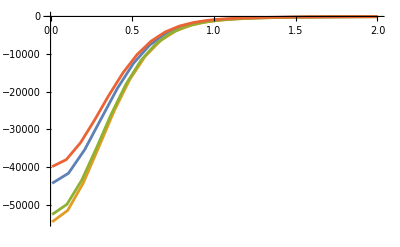

```mathematica
energ=0.01;

(* Integration grid *)
rMa=2.;
grdPerFermi=220;
nGrd=IntegerPart[rMa grdPerFermi];
LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];
(* Plot parameters for the visualization of V(r,r') *)
nR=20;rMi=0.01;thresh=10^-0;

pots={};
Do[
{e0Core,dimerCore}=dCores[[nn]];(*ApproxDimerWF[lambd,dimDimer,nparallelThreads,nDimerWidthSamples,minDimerWidth,maxDimerWidth,midWidthdiff,0];*)

normCore=1./NormTF[dimerCore];
dimCore=Length[dimerCore];


tmp=GetEREP3[lambdaTest^2/4,rMa,nGrd,dimerCore,LECc,energ];
Print["Results core ",nn," :  Norm: ",normCore,"   a_dd = "<>ToString[tmp]];

rR=Range[rMi,rMa,(rMa-rMi)/nR];
nR=Length[rR];
potloc={};
ttp=0;
Do[
cij=dimerCore[[ii]][[1]] dimerCore[[jj]][[1]] dimerCore[[kk]][[1]]  dimerCore[[ll]][[1]] normCore;

potloctmp=
Table[{rR[[i]],cij VlocTF[rR[[i]],lambdaTest^2/4,LECc,0.0,dimerCore[[ii]][[2]],dimerCore[[jj]][[2]],dimerCore[[kk]][[2]],dimerCore[[ll]][[2]],1]}
,{i,Length[rR]}];
AppendTo[potloc,potloctmp]
,{ii,1,dimCore},{jj,1,dimCore},{kk,1,dimCore},{ll,1,dimCore}];

AppendTo[pots,Transpose[{potloc[[1]][[All,1]],Total[potloc[[All,All,2]]]}]];

,{nn,Length[dCores]}];
ListPlot[pots,Joined->True]
```

### maximal-integration-range dependence of the a_dd scattering-length pre/post-diction

λ = 6   C_0(λ) = -1090.8     R_max = 1.2     #(grid points) = 204                a_dd = 1.02404 fm        a_dd/a_aa = 0.227737

λ = 6   C_0(λ) = -1090.8     R_max = 1.62     #(grid points) = 275                a_dd = 3.552 fm        a_dd/a_aa = 0.789938

λ = 6   C_0(λ) = -1090.8     R_max = 2.04     #(grid points) = 346                a_dd = 2.33213 fm        a_dd/a_aa = 0.518649

λ = 6   C_0(λ) = -1090.8     R_max = 2.46     #(grid points) = 418                a_dd = 2.31715 fm        a_dd/a_aa = 0.515315

λ = 6   C_0(λ) = -1090.8     R_max = 2.88     #(grid points) = 489                a_dd = 2.26488 fm        a_dd/a_aa = 0.503692

λ = 6   C_0(λ) = -1090.8     R_max = 3.3     #(grid points) = 561                a_dd = 2.09816 fm        a_dd/a_aa = 0.466613

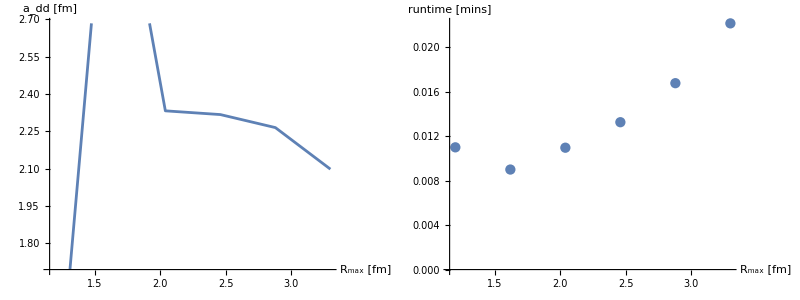

```mathematica
rMaxStart=1.2;
rMaxEnd=3.3;
nbrR=5;

RmaxRange=Range[rMaxStart,rMaxEnd,N[(rMaxEnd-rMaxStart)/nbrR]];
energ=0.001;
grdPerFermi=170;
results={};
runtimes={};
(*SetSharedVariable[results,resultsPhases];*)
Do[
nGrd=IntegerPart[rMa grdPerFermi];
ta=AbsoluteTime[];
tmp=GetEREP3[lambdaTest^2/4,rMa,nGrd,dimerCore,LECc,energ];
tb=AbsoluteTime[];
AppendTo[results,tmp];
AppendTo[runtimes,{rMa,(tb-ta)/60.}];
Print["λ = ",lambdaTest,"   C_0(λ) = ",LECc,"     R_max = ",rMa,"     #(grid points) = ",nGrd,"                a_dd = ",tmp," fm        a_dd/a_aa = ",Style[tmp/(hbar/√(Mm Abs[e0Core])),Red,18]];
,{rMa,RmaxRange}]

Grid[{{ListPlot[Transpose[{RmaxRange,results}],ImageSize->Large,Joined->True,AxesLabel->{"R_max [fm]","a_dd [fm]"}],ListPlot[runtimes,ImageSize->Large,AxesLabel->{"R_max [fm]","runtime [mins]"}]}}]
```